```mathematica
(*Pauli matrices*)
sz=PauliMatrix[3];
sx=PauliMatrix[1];
```

```mathematica
(*Parameters*)
α=1/2;
γ = 1;
```

```mathematica
(*Hamiltonian*)
H= ⅈ α sz + γ sx;
Eigensystem[H]
```

{{-(√3)/2,(√3)/2},{{1/2 (ⅈ-√3),1},{1/2 (ⅈ+√3),1}}}

```mathematica
(*Propagator*)
U= MatrixExp[ -ⅈ H t];
```

```mathematica
U//MatrixForm
```

(Cos[(√3 t)/2]+Sin[(√3 t)/2]/(√3) | -(2 ⅈ Sin[(√3 t)/2])/(√3)
-(2 ⅈ Sin[(√3 t)/2])/(√3) | Cos[(√3 t)/2]-Sin[(√3 t)/2]/(√3))

```mathematica
(*Initial state*)
ψ0={{0},{1}};
```

```mathematica
meansz = FullSimplify[ComplexExpand[ConjugateTranspose[ψ0].ConjugateTranspose[U].sz.U.ψ0]][[1,1]]
```

-Cos[√3 t]+Sin[√3 t]/(√3)

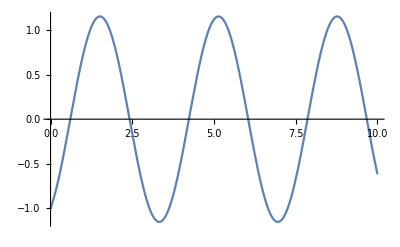

```mathematica
Plot[meansz,{t,0,10}]
```

```mathematica
(*Valor de cada estado propagado en el tiempo*)
meanPg = FullSimplify[ComplexExpand[ConjugateTranspose[ψ0].ConjugateTranspose[U].{{0,0},{0,1}}.U.ψ0]]
meanPe = FullSimplify[ComplexExpand[ConjugateTranspose[ψ0].ConjugateTranspose[U].{{1,0},{0,0}}.U.ψ0]]
```

{{1/3 (2+Cos[√3 t]-√3 Sin[√3 t])}}

{{-2/3 (-1+Cos[√3 t])}}

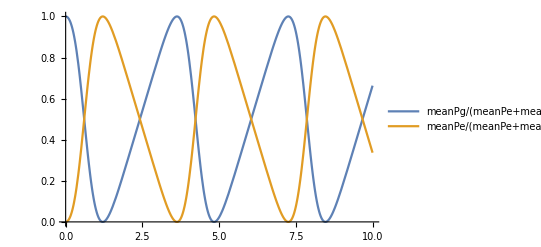

```mathematica
Plot[{meanPg/(meanPe+ meanPg),meanPe/(meanPe+ meanPg)},{t,0,10}, PlotRange->All,PlotLegends->"Expressions"]
```

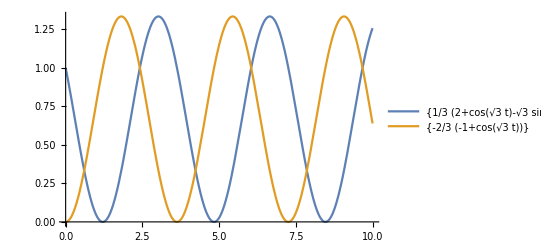

```mathematica
Plot[{meanPg,meanPe},{t,0,10}, PlotRange->All,PlotLegends->"Expressions"]
```